# Carnot Number

## (Input/Output Temperature Difference in Hydroelectric Power Stations)/(Seasonal Temperature Difference in Ocean/River Systems)

## Human Relevance

### Grand Coulee Dam

Hydro electric stations are the oldest form of grid scale power plant

Largest power plant in the US ∼ 7GW

∼2× larger than the second largest power station (Palo Verde - Nuclear)

Roosevelt Reservoir heats up the rivers waters

Much larger impact than factories or traditional power plants which use rivers/streams for cooling

Salmon are particularly sensitive to the temperature of the river

>15°C strains the fish, >20°C can be fatal to the fish

In 2019 ∼1/2 of all 500,00 sockeye salmon returning to the Columbia River basin died because of abnormally high temperatures

https://www.oregonlive.com/environment/2015/07/hot_water_killing_half_of_colu.html

## Approximating The “Carnot Number”

## Heat Drop Across Hydro-plant

### Definitions

η≡Turbine efficiency of power plant⇒(1-η)≈f·10^-1
g≡Gravitational aceleration≈10 m/s^2
h≡Height Difference between upper and lower reservoirs ≈10^2 m
c_p≡Specific heat of water ≈f·10^3 J/(kg·°C)
ṁ≡Flow rate through plant
t≡time 
T≡Temperature

### Governing Eqns.

Power into Heat:	P_H=(1-η)ṁ g h
Work into heat:	W_H=∫_0^Δt P_H ⅆτ=(1-η)ṁ g h Δt
Heat to raise the temp. of water:	ΔQ=c_p(ṁ Δt) ΔT

(1-η)ṁ g h Δt=c_p(ṁ Δt) ΔT
⇒	ΔT=((1-η)g h)/c_p=(f·10^-1·10m/s^2·10^2m)/(f·10^3 J/(kg·°C))=10^-1°C

#### Checking the units:

```mathematica
UnitSimplify[(Quantity[, ("Meters")/("Seconds")^2]*Quantity[, "Meters"])/Quantity[, ("Joules")/("DegreesCelsiusDifference" "Kilograms")]]
```

1 K

## Heat Change Over The Year

### Intuition

We know that river’s in the north build up ice in the winter (≈10^0°C) to being comfortable enough to swim in during the summer (≈10^1°C-f·10^1°C). 
Thus the total temperature change is either 10^1°C-f·10^1°C.

To make a more mathematical guess, consider the temperature variation over the seasons to be a square wave rather than a sinusoid (Its either summer, or winter). Assume that the water in a dam’s reservoir originated entirely from underground aquifers, which were held at a constant temperature.

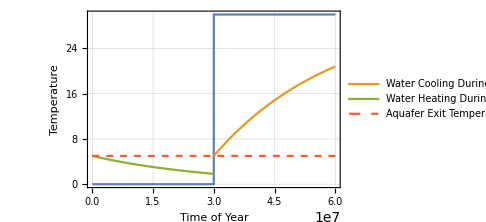

```mathematica
waterTempApprox=Show[
Plot[15(SquareWave[(t+3*10^7)/(6*10^7)]+1),{t,0,6*10^7},Exclusions->None,PlotStyle->ColorData[97,"ColorList"]⟦1⟧,Frame->True,GridLines->Automatic,ImageSize->Medium,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],FrameLabel->{Style["Time of Year",16,Bold],Style["Temperature",16,Bold]}],
Plot[-ⅇ^(-(A h (t-3*10^7))/(c m)) (-5+Subscript[T, a])+Subscript[T, a]/.{Subscript[T, a]->3*10^1,h->10,c->3*1000,A->3*10^8,m-> 3*10^13},{t,3*10^7,6*10^7},PlotStyle->ColorData[97,"ColorList"]⟦2⟧,PlotLegends->{"Water Cooling\nDuring Winter"}],
Plot[-ⅇ^(-(A h t)/(c m)) (-5+Subscript[T, a])+Subscript[T, a]/.{Subscript[T, a]->0,h->10,c->3*1000,A->3*10^8,m-> 3*10^13},{t,0,3*10^7},PlotStyle->ColorData[97,"ColorList"]⟦3⟧,PlotLegends->{"Water Heating\nDuring Summer"}],
Plot[5,{t,0,6*10^7},PlotStyle->{ColorData[97,"ColorList"]⟦4⟧,Dashed},PlotLegends->{"Aquafer Exit\nTemperature"}]
]
```

#### Saving Graphic

```mathematica
Export[NotebookDirectory[]<>"graphics/water_temperature_Approximation.png",waterTempApprox,ImageResolution->500,Background->None]
```

/Users/AlexanderBouman/Desktop/School/Senior-Term3/APh150/carnot_number/graphics/water_temperature_Approximation.png

Average Temperature across Grand Coulee

```mathematica
Mean[tempDiff⟦;;,2⟧]
```

0.790756 °C

Range of Temperature in the Columbia River

```mathematica
(Max[#]-Min[#]&/@{columbiaBelowCouleeData["DatePath"]⟦;;,2⟧})⟦1⟧
```

16.4625 °C

“Carnot Number”

```mathematica
Quantity[0.79076, "DegreesCelsius"]/Quantity[16.4625, "DegreesCelsius"]
```

0.048034

### Definitions

h≡Heat transfer coefficent of Air≈10^W/(m^2 K)
c_p≡Specific heat of water ≈f·10^3 J/(kg·°C)
m≡Mass of body being cooled≈Lake Roosevelt 10^13 kg
A≡Exposed surface area of body being cooled≈Lake Roosevelt f·10^8 m^2
T_a≡Temperature of air ≈f·10 °C  during the summer, 0°C during the winter
T_aq≡Temperature of water in aquafer≈f °C  year round
T_w≡Temperature of water in reservoir
Q≡Heat

### Governing Eqns.

Newtonian cooling:		(∂Q)/(∂t)=h A (T_a-T_w(t))
Heat to change the temp. of water:		∂Q=c_p m ∂T_w

(∂T)/(∂t)=(h A)/(c_p m) (T_a-T_w(t))
T_w(t)=T_a-ⅇ^(-(A h t)/(c m)) (T_aq-T_a)

Summer

T_w(t)=f·10 °C-exp(-(f·10^8 m^2 * 10 W/(m^2 K)  * t)/(f·10^3 J/(kg·°C)* 10^13 kg)) (f °C-f·10 °C)
T_w(t)=f·10 °C-exp(-t*10^-7) (f·10 °C)
After 6 months t≈f·10^7 ⇒
T_w(t)=f·10 °C-exp(-f) (f·10 °C)=f·10 °C-f·10^-2* (f·10 °C)=f·10 °C

Winter

T_w(t)=0 °C-exp(-(f·10^8 m^2 * 10 W/(m^2 K)  * t)/(f·10^3 J/(kg·°C)* 10^13 kg)) (f °C-0 °C)
T_w(t)=-exp(-t*10^-7) (f °C)
After 6 months t≈f·10^7 ⇒
T_w(t)=f·10^-2* (f °C)=10^-1 °C

#### Checking the units:

```mathematica
UnitSimplify[Exp[(Quantity[, ("Meters")^2]*Quantity[, ("Watts")/("KelvinsDifference" ("Meters")^2)]*Quantity[, "Seconds"])/(Quantity[, ("Joules")/("DegreesCelsiusDifference" "Kilograms")]*Quantity[, "Kilograms"])]*Quantity[, "DegreesCelsiusDifference"]]
```

### Approximate Carnot Number

(10^-1°C)/(f·10°C)=f·10^-2

## What The Data Says

## Columbia River - Grand Coulee Dam

### Importing Data

#### Below Coulee

```mathematica
filename=NotebookDirectory[]<>"river_temperatures/columbia_below_Coulee.csv";
temp=Import[filename,"Data"];
temp=Replace[temp,x_List:>DeleteCases[x,{}],{0,Infinity}];
temp=({First[#],#⟦Length[#]-1⟧}&/@temp)⟦2;;-6⟧;
temp={(DateObject[{2019,1,1,0,0,0}]+Quantity[#-1,"Days"])&/@temp⟦;;,1⟧,Quantity[#,"DegreesCelsius"]&/@temp⟦;;,2⟧}ᵀ;
(*columbiaBelowCouleeData=TimeSeriesResample[TimeSeries[temp],28800];*)
columbiaBelowCouleeData=TimeSeries[temp];
```

#### Above Coulee

```mathematica
filename=NotebookDirectory[]<>"river_temperatures/columbia_above_Coulee.csv";
temp=Import[filename,"Data"];
temp=Replace[temp,x_List:>DeleteCases[x,{}],{0,Infinity}];
temp=({First[#],#⟦Length[#]-1⟧}&/@temp)⟦2;;-6⟧;
temp={(DateObject[{2019,1,1,0,0,0}]+Quantity[#-1,"Days"])&/@temp⟦;;,1⟧,Quantity[#,"DegreesCelsius"]&/@temp⟦;;,2⟧}ᵀ;
(*columbiaAboveCouleeData=TimeSeriesResample[TimeSeries[temp],28800];*)
columbiaAboveCouleeData=TimeSeries[temp];
```

#### Difference Across

```mathematica
tempDiff=columbiaAboveCouleeData;
tempDiff={columbiaAboveCouleeData["DatePath"]⟦;;,1⟧,
columbiaAboveCouleeData["DatePath"]⟦;;,2⟧-columbiaBelowCouleeData["DatePath"]⟦;;,2⟧}ᵀ;
```

### Saving Data

```mathematica
saveData=ConstantArray[0,{Length[columbiaBelowCouleeData["DatePath"]], 4}];
saveData⟦;;,1⟧=DateString[#]&/@columbiaBelowCouleeData["DatePath"]⟦;;,1⟧;
saveData⟦;;,2⟧=QuantityMagnitude[#]&/@columbiaBelowCouleeData["DatePath"]⟦;;,2⟧;
saveData⟦;;,3⟧=QuantityMagnitude[#]&/@columbiaAboveCouleeData["DatePath"]⟦;;,2⟧;
saveData⟦;;,4⟧=QuantityMagnitude[#]&/@tempDiff⟦;;,2⟧;
saveData=Join[{{"Date","Temperature(°C) Above Grand Coulee Dam", "Temperature(°C) Below Grand Coulee Dam",, "Temperature Difference Across Dam"}},saveData];
Export[NotebookDirectory[]<>"carnot_number/river_temperatures/columbia_river_Grand_Coulee_Dam.csv",saveData];
```

### Plotting Data

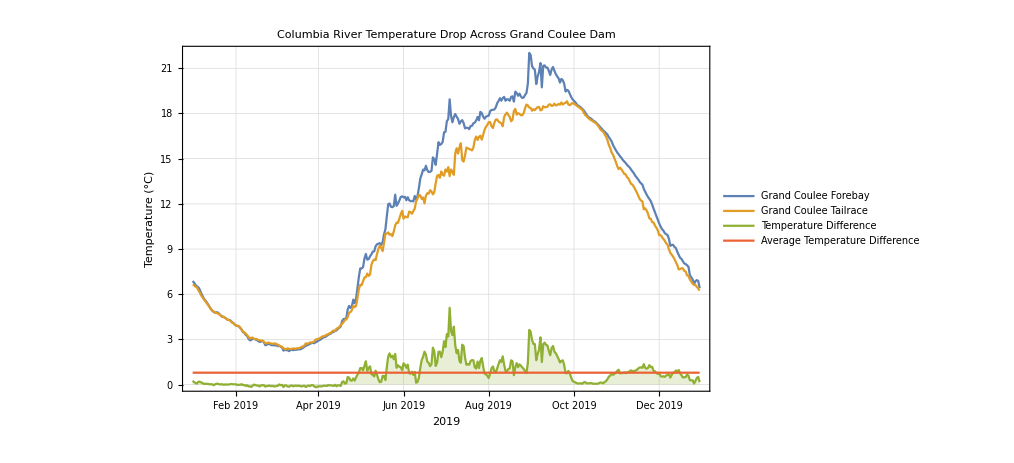

```mathematica
columbiaRiverTemp=Show[
DateListPlot[{columbiaAboveCouleeData,columbiaBelowCouleeData},PlotRange->All,GridLines->Automatic,ImageSize->{750,500},PlotLegends->{"Grand Coulee Forebay","Grand Coulee Tailrace"},PlotLabel->Style["Columbia River Temperature Drop Across Grand Coulee Dam",24],FrameLabel->{Style["2019",16,Bold],Style["Temperature (°C)",16,Bold]}],
DateListPlot[{tempDiff},PlotRange->All,FrameLabel->{"2019","Temperature (°C)"},ImageSize->Large,Filling->Axis,PlotStyle->ColorData[97,"ColorList"]⟦3⟧,PlotLegends->{"Temperature Difference"}],
DateListPlot[{tempDiff⟦;;,1⟧,ConstantArray[Mean[tempDiff⟦;;,2⟧],Length[tempDiff]]}ᵀ,PlotStyle->ColorData[97,"ColorList"]⟦4⟧,PlotLegends->{"Average Temperature\nDifference"}]
]
```

#### Saving Graphic

```mathematica
Export[NotebookDirectory[]<>"graphics/Columbia_river_Grand_Coulee_temp.png",columbiaRiverTemp,ImageResolution->500,Background->None]
```

/Users/AlexanderBouman/Desktop/School/Senior-Term3/APh150/carnot_number/graphics/Columbia_river_Grand_Coulee_temp.png

Average Temperature across Grand Coulee

```mathematica
Mean[tempDiff⟦;;,2⟧]
```

0.790756 °C

Range of Temperature in the Columbia River

```mathematica
(Max[#]-Min[#]&/@{columbiaBelowCouleeData["DatePath"]⟦;;,2⟧})⟦1⟧
```

16.4625 °C

“Carnot Number”

```mathematica
Quantity[0.79076, "DegreesCelsius"]/Quantity[16.4625, "DegreesCelsius"]
```

0.048034

### Data Source

"Columbia Basin Conditions for Temperature, Dissolved Gas Percent and Spill Percent"
⇒	http://www.cbr.washington.edu/dart/query/basin_conditions
Columbia Basin Research
School of Aquatic & Fishery Sciences
University of Washington
1325 4th Avenue, Suite 1515
Seattle, WA 98101